```mathematica
imgs1 = -Graphics--Graphics-;
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

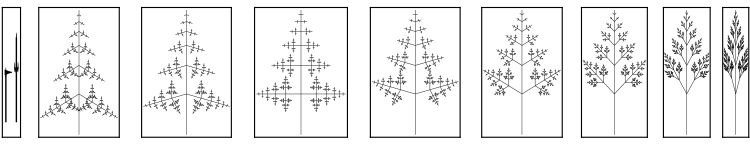

-Graphics-

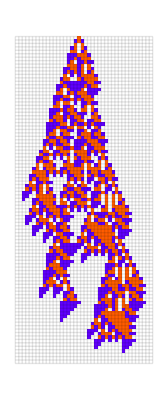

-Graphics-

-Graphics-

### Keepers

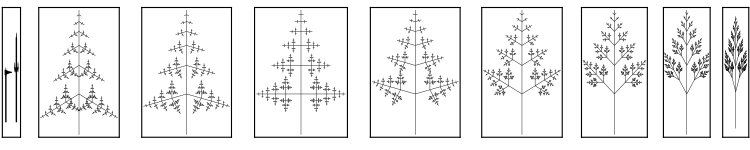
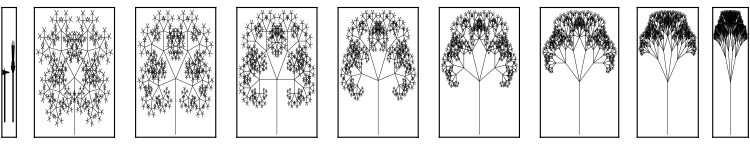
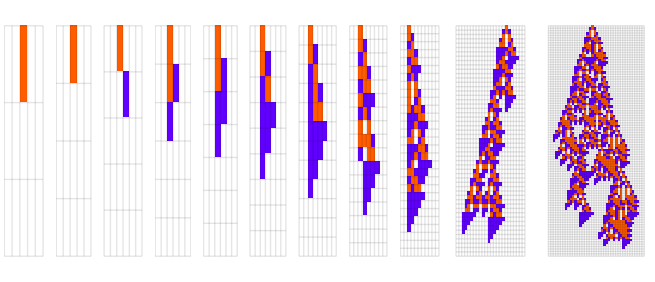
```mathematica
imgs = { -Graphics-, 
 -Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-, -Graphics-};
```

```mathematica
ImageCollage[imgs, Background->White]
```

-Graphics-

```mathematica
ByteCount[imgs]
```

21818360

### Keepers 2

```mathematica
imgs[[3]]
```

-Graphics-

```mathematica
s2 = Import["Projects/Wolfram/Biology/BioCourse/shell2.jpeg"]
```

-Graphics-

```mathematica
pigs = {-Graphics-, -Graphics-, -Graphics-, -Graphics-};
```

```mathematica
GraphicsGrid[Partition[pigs, 2], Background->White]
```

-Graphics-

```mathematica
rpigs = {-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-};
```

```mathematica
GraphicsGrid[Partition[rpigs[[{1, 3, 4, 2}]], 2], Background->White]
```

-Graphics-

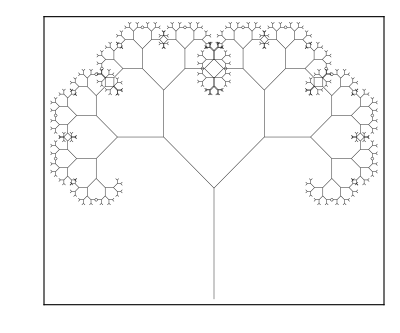

-Graphics-

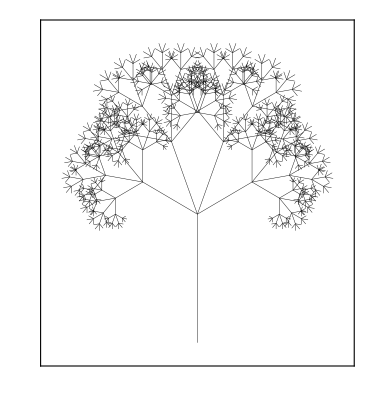

-Graphics-

```mathematica
ls
```

ls

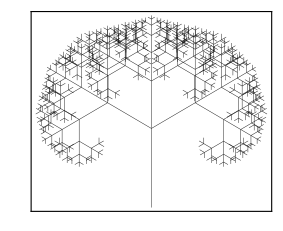
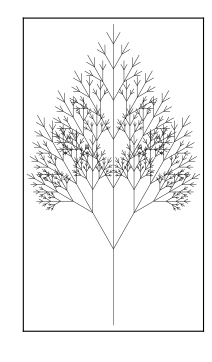
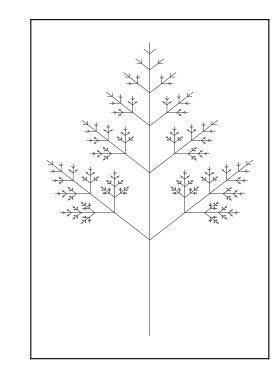
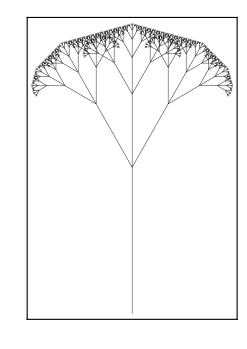
```mathematica
ls2 = {-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
GraphicsGrid[Partition[Show[#,ImageSize->{100, 200}, Frame->False]&/@ls,2], Frame->True]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

GraphicsGrid::list: Partition[ls,2] is not a list of lists.

GraphicsGrid[Partition[ls,2],Frame→True]

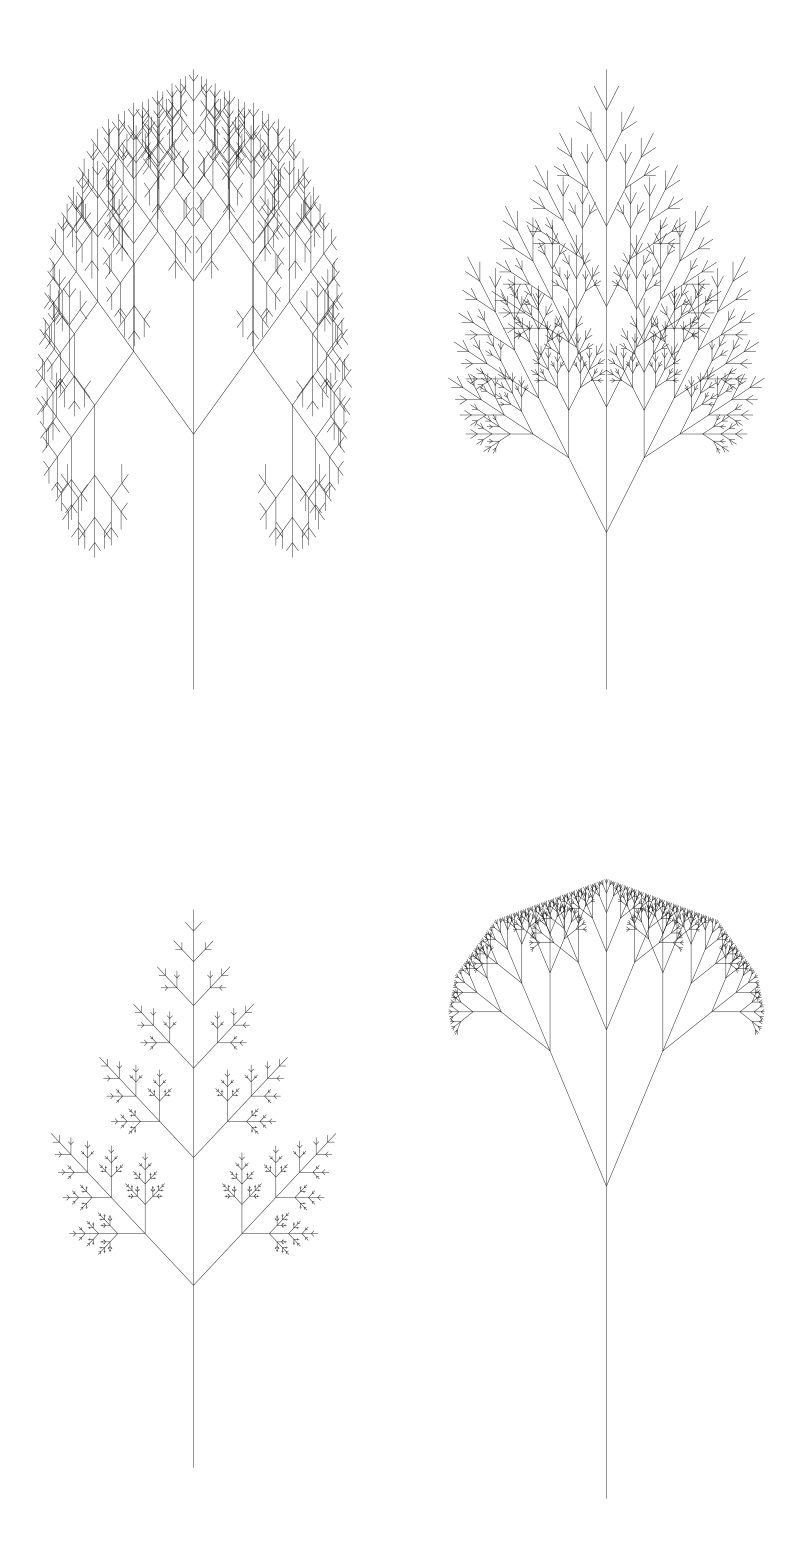

```mathematica
GraphicsGrid[Partition[Show[#,ImageSize->{100, 200}, Frame->False]&/@ls2,2], Frame->True]
```

```mathematica
rls = {-Graphics-,-Graphics-, -Graphics-, -Graphics-};
```

```mathematica
GraphicsGrid[Partition[rls, 2], Frame->True, ImageSize->Medium]
```

-Graphics-

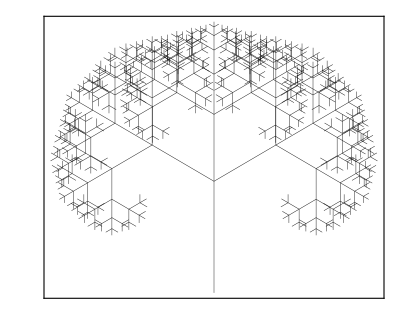

-Graphics-

-Graphics-

```mathematica
evopat = -Graphics-;
```

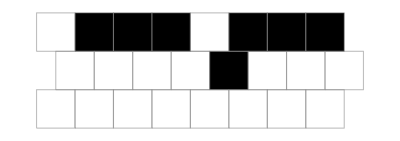
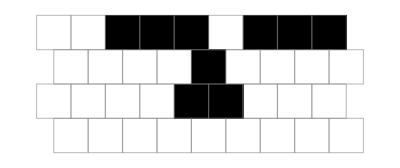
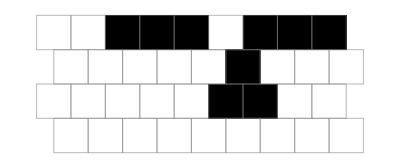
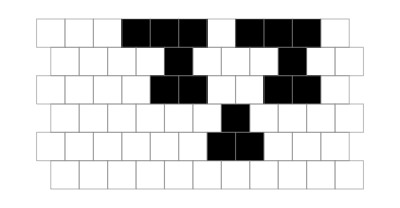
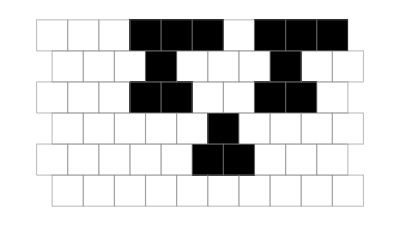
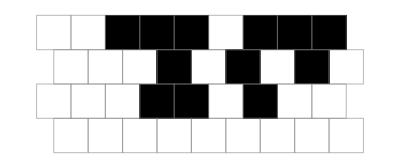
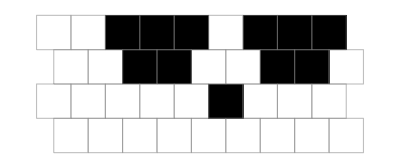
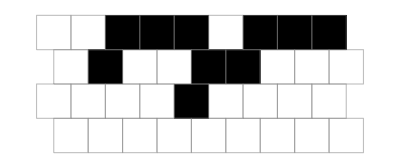

```mathematica
Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{Automatic,(2+key[[1]])10}]
&@First[Union[CellularAutomaton[{#,2,3/2},{{1,1,1,0,1,1,1},0},
key[[1]]]&/@rules]]
],sublevels]];
Graph[res,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
]
```

```mathematica
Rasterize[]
```

-Graphics-

```mathematica
multiimg = -Graphics-;
```

```mathematica
multiimg2 = -Graphics-;
```

```mathematica
d3 = -Graphics-;
```

```mathematica
Head[]
```

Graph

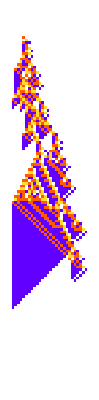
```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

-Graphics- -Graphics- -Graphics- -Graphics-

### grid

```mathematica
imgs[[3]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[pigs, 2], Background->White]
```

-Graphics-

```mathematica
Grid[{{imgs[[3]], s2, {-Graphics-, ""}}}]
```

-Graphics- | -Graphics- | {-Graphics-,}

```mathematica
med = With[{ru={299459058088077823758143088095350287424,4,1}},GraphicsRow[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2]]];
```

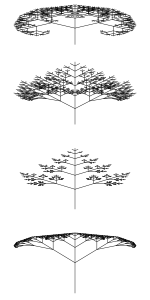
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Column[{Row[{Column[{
Row[{imgs[[3]], Show[s2, ImageSize->200]}],
GraphicsRow[pigs, Background->White, ImageSize->280], GraphicsRow[rpigs[[{1, 3, 4, 2}]], Background->White, ImageSize->280]}], GraphicsColumn[Show[#, Frame->False]&/@ls2, Frame->True, ImageSize->{150, 300}], GraphicsColumn[Show[#, Frame->False]&/@rls, Frame->True, ImageSize->{150, 300}]}], Row[{evopat,d3}], Row[{med, multiimg2}]}]
```

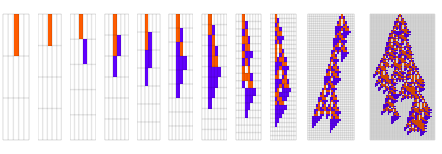
```mathematica
{{{{-Graphics--Graphics-}, {-Graphics-}, {-Graphics-}}-Graphics--Graphics-}, {-Graphics--Graphics-}, {-Graphics--Graphics-}}
```

-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Row[{Row[{Column[{
Row[{imgs[[3]], Show[s2, ImageSize->200]}],
GraphicsRow[pigs, Background->White, ImageSize->280], GraphicsRow[rpigs[[{1, 3, 4, 2}]], Background->White, ImageSize->280]}], GraphicsColumn[Show[#, Frame->False]&/@ls2, Frame->True, ImageSize->{150, 300}], GraphicsColumn[Show[#, Frame->False]&/@rls, Frame->True, ImageSize->{150, 300}]}], GraphicsColumn[{evopat,med}], GraphicsColumn[{d3,multiimg2}]}]
```

-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
GraphicsRow[pigs, Background->White, ImageSize->280], GraphicsRow[rpigs[[{1, 3, 4, 2}]], Background->White, ImageSize->280]]
```

Column[-Graphics-,-Graphics-]

```mathematica
GraphicsGrid[Transpose[{Show[#, ImageSize->500]&/@pigs, Show[#, ImageSize->500]&/@rpigs[[{1, 3, 4, 2}]], Show[#, ImageSize->500, AspectRatio->1]&/@ls2, Show[#, ImageSize->500, AspectRatio->1, Frame->True, FrameTicks->False]&/@rls}], Background->White]
```

-Graphics-